{root→701.218}

-100.+618.051 (-0.025+r)^0.5

1298.16 (0.0258-10. r)^8

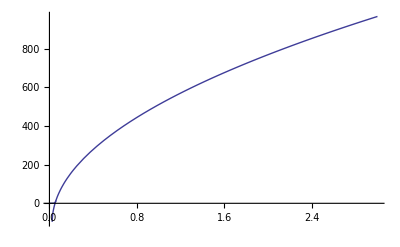

{7.40125}

```mathematica
Clear[r,Cd,pow];
(* everything in meters and kilograms *)
g = 9.81 ;(*m/s2*)
ps =1000; (*kg/m3*)
p =  1.007;(*kg/m3*)
Cd= 0.4;
eq=(((4 g 2(r))/(3 Cd))*((ps-p)/p))^(0.58)-root;
(*eq = a+b r ^(root);*)
pars = {root};
sol=FindFit[X,eq, pars, r]
(*sol={root->100};*)
eq=-100+618.0508659786002 (r-0.025)^0.50;
smalleq=(2.45*(10r-0.0258))^8;
eq/.sol//FullSimplify
smalleq//FullSimplify
Solve[eq==smalleq,r];
plot=Plot[eq/.sol, {r, 0.01, 3}];
smallplot=Plot[smalleq,{r,0,0.065}];
points=ListPlot[{{0.05, 7}, {0.1, 70}, {1, 550}}, Joined->True];
Show[plot,smallplot]
smalleq/.r->{0.055}
```

```mathematica
(0.0258-10. r)^8/.r->0.05
```

0.00255677

```mathematica
(0.0258-10. 0.55)^8
```

806427.

```mathematica
1.5 /27
```

0.0555556

```mathematica
1.5/29.4
```

0.0510204

```mathematica
1.5 / 60
```

0.025

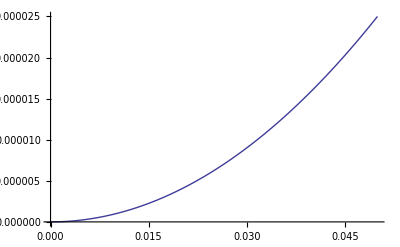

```mathematica
Plot[0.01x^2,{x,0,0.05}]
```

```mathematica
X=ReadList[StringToStream["
0.1              0.27
0.2              0.72
0.3              1.17
0.4              1.62
0.5              2.06
0.6              2.47
0.7              2.87
0.8              3.27
0.9              3.67
1.0              4.03
1.2              4.64
1.4              5.17
1.6              5.65
1.8              6.09
2.0              6.49
2.2              6.90
2.4              7.27
2.6              7.57
2.8              7.82
3.0              8.06
3.2              8.26
"],{Number,Number}]
```

{{0.1,0.27},{0.2,0.72},{0.3,1.17},{0.4,1.62},{0.5,2.06},{0.6,2.47},{0.7,2.87},{0.8,3.27},{0.9,3.67},{1.,4.03},{1.2,4.64},{1.4,5.17},{1.6,5.65},{1.8,6.09},{2.,6.49},{2.2,6.9},{2.4,7.27},{2.6,7.57},{2.8,7.82},{3.,8.06},{3.2,8.26}}

```mathematica
X
```

{{0.1,0.27},{0.2,0.72},{0.3,1.17},{0.4,1.62},{0.5,2.06},{0.6,2.47},{0.7,2.87},{0.8,3.27},{0.9,3.67},{1.,4.03},{1.2,4.64},{1.4,5.17},{1.6,5.65},{1.8,6.09},{2.,6.49},{2.2,6.9},{2.4,7.27},{2.6,7.57},{2.8,7.82},{3.,8.06},{3.2,8.26}}

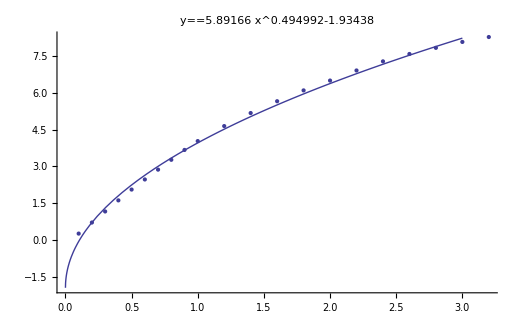

```mathematica
Show[ListPlot[X],Plot[a+b x^c/.sol,{x,0,3}], PlotLabel->y==a+b x^c/.sol]
```

```mathematica
sol=FindFit[X,a+b x^c,{a,b,c},x]
```

{a→-1.93438,b→5.89166,c→0.494992}

```mathematica
a+b x^c/.sol
```

-1.93438+5.89166 x^0.494992

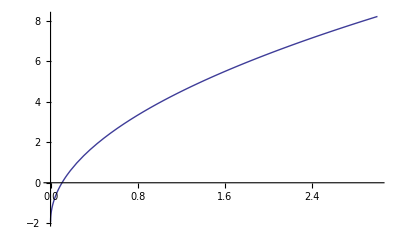

```mathematica
Plot[100(a+b x^c)/.sol,{x,0,3}]
```